```mathematica
Quit
```

# EDA

### Explicacion ELO

initialElo
Description: The initial ELO rating assigned to every team before any matches are processed. It represents a baseline level from which teams can move up or down based on their performance.
Example Value: 1500

kFactor
Description: A constant that determines the magnitude of rating changes after each match. A higher K-factor results in larger changes, making the system more sensitive to individual match results.
Example Value: 30

expectedScore[ratingA_, ratingB_]
Description: A function that calculates the expected probability of a team (with a certain ELO rating) winning a match against another team (with a different ELO rating). The expected score is a value between 0 and 1.
Inputs:
ratingA_: The ELO rating of team A.
ratingB_: The ELO rating of team B.

updateElo[currentRating_, expected_, actual_]
Description: A function that updates a team’s ELO rating based on its current rating, the expected match outcome, and the actual match outcome.
Inputs:
currentRating_: The team’s current ELO rating.
expected_: The expected outcome calculated by expectedScore.
actual_: The actual outcome of the match (1 for a win, 0.5 for a draw, 0 for a loss).

eloRatings
Description: A dictionary (or association) that stores the ELO ratings for all teams. The keys are team names, and the values are their corresponding ELO ratings.
Example Value: <|”Liverpool” -> 1520, “Man City” -> 1480, ...|>

matches
Description: A list of match data where each match is represented as an association with details like the home team, away team, and goals scored by each team. This is a simplified representation of your actual match data.
Example Value:
wolfram
Copy code
{
  {“HomeTeam” -> “Liverpool”, “AwayTeam” -> “Man City”, “HomeGoals” -> 2, “AwayGoals” -> 1},
  {“HomeTeam” -> “Chelsea”, “AwayTeam” -> “Arsenal”, “HomeGoals” -> 0, “AwayGoals” -> 3},
  ...
}

homeTeam
Description: A variable that stores the name of the home team for the current match being processed.
Example Value: “Liverpool”

awayTeam
Description: A variable that stores the name of the away team for the current match being processed.
Example Value: “Man City”

homeGoals
Description: A variable that stores the number of goals scored by the home team in the current match.
Example Value: 2

awayGoals
Description: A variable that stores the number of goals scored by the away team in the current match.
Example Value: 1

homeRating
Description: The current ELO rating of the home team before the match result is applied.
Example Value: 1500

awayRating
Description: The current ELO rating of the away team before the match result is applied.
Example Value: 1500

homeExpected
Description: The expected score for the home team in the match, based on the current ELO ratings of both teams.
Example Value: 0.52

awayExpected
Description: The expected score for the away team in the match, based on the current ELO ratings of both teams.
Example Value: 0.48

homeActual
Description: The actual score for the home team in the match, determined by the match result. It can be 1 for a win, 0.5 for a draw, or 0 for a loss.
Example Value: 1

awayActual
Description: The actual score for the away team in the match, determined by the match result. It can be 1 for a win, 0.5 for a draw, or 0 for a loss.
Example Value: 0

finalEloRatings
Description: A list of the final ELO ratings for all teams, sorted in descending order. Each entry includes the team name and its final ELO rating.
Example Value:
wolfram
Copy code
{
  {“Liverpool”, 1765.69},
  {“Man City”, 1716.65},
  ...
}

Summary:
Initial Variables (initialElo, kFactor): Set up the starting conditions.
Functions (expectedScore, updateElo): Define the calculations for ELO ratings.
Match Processing Variables: Handle each match, update ratings, and store results.
Final Result (finalEloRatings): Present the sorted ELO ratings of the teams after processing all matches.

## Database

#### Information about variables

Notes for Football Data

All data is in csv format, ready for use within standard spreadsheet applications. Please note that some abbreviations are no longer in use (in particular odds from specific bookmakers no longer used) and refer to data collected in earlier seasons. For a current list of what bookmakers are included in the dataset please visit http://www.football-data.co.uk/matches.php

Key to results data:

Div = League Division
Date = Match Date (dd/mm/yy)
Time = Time of match kick off
HomeTeam = Home Team
AwayTeam = Away Team
FTHG and HG = Full Time Home Team Goals
FTAG and AG = Full Time Away Team Goals
FTR and Res = Full Time Result (H=Home Win, D=Draw, A=Away Win)
HTHG = Half Time Home Team Goals
HTAG = Half Time Away Team Goals
HTR = Half Time Result (H=Home Win, D=Draw, A=Away Win)

Match Statistics (where available)
Attendance = Crowd Attendance
Referee = Match Referee
HS = Home Team Shots
AS = Away Team Shots
HST = Home Team Shots on Target
AST = Away Team Shots on Target
HHW = Home Team Hit Woodwork
AHW = Away Team Hit Woodwork
HC = Home Team Corners
AC = Away Team Corners
HF = Home Team Fouls Committed
AF = Away Team Fouls Committed
HFKC = Home Team Free Kicks Conceded
AFKC = Away Team Free Kicks Conceded
HO = Home Team Offsides
AO = Away Team Offsides
HY = Home Team Yellow Cards
AY = Away Team Yellow Cards
HR = Home Team Red Cards
AR = Away Team Red Cards
HBP = Home Team Bookings Points (10 = yellow, 25 = red)
ABP = Away Team Bookings Points (10 = yellow, 25 = red)

Note that Free Kicks Conceeded includes fouls, offsides and any other offense commmitted and will always be equal to or higher than the number of fouls. Fouls make up the vast majority of Free Kicks Conceded. Free Kicks Conceded are shown when specific data on Fouls are not available (France 2nd, Belgium 1st and Greece 1st divisions).

Note also that English and Scottish yellow cards do not include the initial yellow card when a second is shown to a player converting it into a red, but this is included as a yellow (plus red) for European games.

Key to 1X2 (match) betting odds data:

B365H = Bet365 home win odds
B365D = Bet365 draw odds
B365A = Bet365 away win odds
BSH = Blue Square home win odds
BSD = Blue Square draw odds
BSA = Blue Square away win odds
BWH = Bet&Win home win odds
BWD = Bet&Win draw odds
BWA = Bet&Win away win odds
GBH = Gamebookers home win odds
GBD = Gamebookers draw odds
GBA = Gamebookers away win odds
IWH = Interwetten home win odds
IWD = Interwetten draw odds
IWA = Interwetten away win odds
LBH = Ladbrokes home win odds
LBD = Ladbrokes draw odds
LBA = Ladbrokes away win odds
PSH and PH = Pinnacle home win odds
PSD and PD = Pinnacle draw odds
PSA and PA = Pinnacle away win odds
SOH = Sporting Odds home win odds
SOD = Sporting Odds draw odds
SOA = Sporting Odds away win odds
SBH = Sportingbet home win odds
SBD = Sportingbet draw odds
SBA = Sportingbet away win odds
SJH = Stan James home win odds
SJD = Stan James draw odds
SJA = Stan James away win odds
SYH = Stanleybet home win odds
SYD = Stanleybet draw odds
SYA = Stanleybet away win odds
VCH = VC Bet home win odds
VCD = VC Bet draw odds
VCA = VC Bet away win odds
WHH = William Hill home win odds
WHD = William Hill draw odds
WHA = William Hill away win odds

Bb1X2 = Number of BetBrain bookmakers used to calculate match odds averages and maximums
BbMxH = Betbrain maximum home win odds
BbAvH = Betbrain average home win odds
BbMxD = Betbrain maximum draw odds
BbAvD = Betbrain average draw win odds
BbMxA = Betbrain maximum away win odds
BbAvA = Betbrain average away win odds

MaxH = Market maximum home win odds
MaxD = Market maximum draw win odds
MaxA = Market maximum away win odds
AvgH = Market average home win odds
AvgD = Market average draw win odds
AvgA = Market average away win odds

Key to total goals betting odds:

BbOU = Number of BetBrain bookmakers used to calculate over/under 2.5 goals (total goals) averages and maximums
BbMx>2.5 = Betbrain maximum over 2.5 goals
BbAv>2.5 = Betbrain average over 2.5 goals
BbMx<2.5 = Betbrain maximum under 2.5 goals
BbAv<2.5 = Betbrain average under 2.5 goals

GB>2.5 = Gamebookers over 2.5 goals
GB<2.5 = Gamebookers under 2.5 goals
B365>2.5 = Bet365 over 2.5 goals
B365<2.5 = Bet365 under 2.5 goals
P>2.5 = Pinnacle over 2.5 goals
P<2.5 = Pinnacle under 2.5 goals
Max>2.5 = Market maximum over 2.5 goals
Max<2.5 = Market maximum under 2.5 goals
Avg>2.5 = Market average over 2.5 goals
Avg<2.5 = Market average under 2.5 goals

Key to Asian handicap betting odds:

BbAH = Number of BetBrain bookmakers used to Asian handicap averages and maximums
BbAHh = Betbrain size of handicap (home team)
AHh = Market size of handicap (home team) (since 2019/2020)
BbMxAHH = Betbrain maximum Asian handicap home team odds
BbAvAHH = Betbrain average Asian handicap home team odds
BbMxAHA = Betbrain maximum Asian handicap away team odds
BbAvAHA = Betbrain average Asian handicap away team odds

GBAHH = Gamebookers Asian handicap home team odds
GBAHA = Gamebookers Asian handicap away team odds
GBAH = Gamebookers size of handicap (home team)
LBAHH = Ladbrokes Asian handicap home team odds
LBAHA = Ladbrokes Asian handicap away team odds
LBAH = Ladbrokes size of handicap (home team)
B365AHH = Bet365 Asian handicap home team odds
B365AHA = Bet365 Asian handicap away team odds
B365AH = Bet365 size of handicap (home team)
PAHH = Pinnacle Asian handicap home team odds
PAHA = Pinnacle Asian handicap away team odds
MaxAHH = Market maximum Asian handicap home team odds
MaxAHA = Market maximum Asian handicap away team odds	
AvgAHH = Market average Asian handicap home team odds
AvgAHA = Market average Asian handicap away team odds


Closing odds (last odds before match starts)
As above but with an additional “C” character following the bookmaker abbreviation/Max/Avg
Football-Data would like to acknowledge the following sources which have been utilised in the compilation of Football-Data’s results and odds files.
Current results (full time, half time)
XScores - http://www.xscores .com
Match statistics
BBC, ESPN Soccer, Bundesliga.de, Gazzetta.it and Football.fr
Bookmakers betting odds
Individual bookmakers
Betting odds for weekend games are collected Friday afternoons, and on Tuesday afternoons for midweek games.
Additional match statistics (corners, shots, bookings, referee etc.) for the 2000/01 and 2001/02 seasons for the English, Scottish and German leagues were provided by Sports.com (now under new ownership and no longer available).

#### Database construction

```mathematica
chooseLeague = "L";
(*Importación de los datos*)
If[chooseLeague=="La Liga",
	data2425list = Import["https://www.football-data.co.uk/mmz4281/2425/SP1.csv", "CSV"];
	data2324list = Import["https://www.football-data.co.uk/mmz4281/2324/SP1.csv", "CSV"];
	data2223list = Import["https://www.football-data.co.uk/mmz4281/2223/SP1.csv", "CSV"];
	data2122list = Import["https://www.football-data.co.uk/mmz4281/2122/SP1.csv", "CSV"];
	data2021list = Import["https://www.football-data.co.uk/mmz4281/2021/SP1.csv", "CSV"];
	data1920list = Import["https://www.football-data.co.uk/mmz4281/1920/SP1.csv", "CSV"];
	,
	(*Importación de los datos*)
	data2425list=Import["https://www.football-data.co.uk/mmz4281/2425/E0.csv","CSV"];
	data2324list=Import["https://www.football-data.co.uk/mmz4281/2324/E0.csv","CSV"];
	data2223list=Import["https://www.football-data.co.uk/mmz4281/2223/E0.csv","CSV"];
	data2122list=Import["https://www.football-data.co.uk/mmz4281/2122/E0.csv","CSV"];
	data2021list=Import["https://www.football-data.co.uk/mmz4281/2021/E0.csv","CSV"];
	data1920list=Import["https://www.football-data.co.uk/mmz4281/1920/E0.csv","CSV"];
	];
	
(* Corroborar que todas las variables sean comunes entre bases de datos *)
(*
Complement[data2425list[[1]], data2324list[[1]]];
Complement[data2324list[[1]], data2425list[[1]]];
*)

(* Eliminar variables que no sean comunes entre bases de datos *)
indices2425 = Reverse[Sort[Flatten[Position[data2425list[[1]], #] & /@ Complement[data2425list[[1]], data2324list[[1]]]]]];
indices2324 = Reverse[Sort[Flatten[Position[data2324list[[1]], #] & /@ Complement[data2324list[[1]], data2425list[[1]]]]]];
indices2223 = Reverse[Sort[Flatten[Position[data2223list[[1]], #] & /@ Complement[data2223list[[1]], data2425list[[1]]]]]];
indices2122 = Reverse[Sort[Flatten[Position[data2223list[[1]], #] & /@ Complement[data2122list[[1]], data2425list[[1]]]]]];
indices2021 = Reverse[Sort[Flatten[Position[data2021list[[1]], #] & /@ Complement[data2021list[[1]], data2425list[[1]]]]]];
indices1920 = Reverse[Sort[Flatten[Position[data2021list[[1]], #] & /@ Complement[data1920list[[1]], data2425list[[1]]]]]];

data2425list = data2425list[[All, Complement[Range[Length[data2425list[[1]]]], indices2425]]];
data2324list = data2324list[[All, Complement[Range[Length[data2324list[[1]]]], indices2324]]];
data2223list = data2223list[[All, Complement[Range[Length[data2223list[[1]]]], indices2223]]];
data2122list = data2122list[[All, Complement[Range[Length[data2122list[[1]]]], indices2122]]];
data2021list = data2021list[[All, Complement[Range[Length[data2021list[[1]]]], indices2021]]];
data1920list = data1920list[[All, Complement[Range[Length[data1920list[[1]]]], indices1920]]];

(*Obtener los nombres de las columnas de uno de los dataframes*)
columnNames=First[data2425list];

(*Eliminar la primera fila de cada dataframe (los encabezados) y añadir la columna Season*)
data2425list=Append[#,"2425"]&/@Rest[data2425list];
data2324list=Append[#,"2324"]&/@Rest[data2324list];
data2223list=Append[#,"2223"]&/@Rest[data2223list];
data2122list=Append[#,"2122"]&/@Rest[data2122list];
data2021list=Append[#,"2021"]&/@Rest[data2021list];
data1920list=Append[#,"1920"]&/@Rest[data1920list];

(*Unir los dataframes*)
dataList=Join[{Append[columnNames,"Season"]},data2425list,data2324list,data2223list,data2122list,data2021list,data1920list];
dateList = DateObject[{ToExpression[StringTake[#, {7, 10}]], 
                                ToExpression[StringTake[#, {4, 5}]], 
                                ToExpression[StringTake[#, {1, 2}]]}] & /@ 
                                (Rest[dataList[[All,2]]]);
dataAssociation=AssociationThread[dataList[[1]]->#]&/@Rest[dataList];
dataAssociation=MapThread[Append[#1, "DateConverted" -> #2] &, {dataAssociation, dateList}];
(* Working with dataset *)
dataDS = Dataset[dataAssociation];
(*dataDS = SortBy[dataDS,#DateConverted &];*)

(*(* Dividir los datos en conjuntos de entrenamiento y prueba *)
dataTrainingSetDS = dataDS[Select[#DateConverted<=DateObject[{2023,07,15},"Day"]&]];
dataTestSetDS = dataDS[Select[DateObject[{2024,07,15},"Day"]>#DateConverted>DateObject[{2023,07,15},"Day"]&]];*)
```

```mathematica
Export["C:/Users/geral/OneDrive - Universidad del Pacífico/Trabajos/CMA/data_ligainglesa_chatGPT.csv",dataDS];
```

```mathematica
(* Inicializar parámetros ELO *)
initialElo = 1500;
kFactor = 10;
(* Función para calcular la puntuación esperada *)
expectedScore[ratingA_, ratingB_] := 1/(1 + 10^((ratingB - ratingA)/400));
(* Función para actualizar la calificación ELO *)
updateElo[currentRating_, expected_, actual_] := currentRating + kFactor * (actual - expected);
(* Inicializar diccionario de calificaciones ELO *)
eloRatings = <||>;
(* Procesar cada partido para actualizar las calificaciones ELO *)
dataDS[All, 
  Function[match, 
   Module[{homeTeam, awayTeam, homeGoals, awayGoals, homeRating, 
     awayRating, homeExpected, awayExpected, homeActual, awayActual},
    
    homeTeam = match["HomeTeam"];
    awayTeam = match["AwayTeam"];
    homeGoals = match["FTHG"];
    awayGoals = match["FTAG"];
    
    (* Inicializar calificaciones ELO si los equipos no están calificados *)
    If[! KeyExistsQ[eloRatings, homeTeam], 
     eloRatings[homeTeam] = initialElo];
    If[! KeyExistsQ[eloRatings, awayTeam], 
     eloRatings[awayTeam] = initialElo];
    
    (* Obtener calificaciones actuales *)
    homeRating = eloRatings[homeTeam];
    awayRating = eloRatings[awayTeam];
    
    (* Calcular puntuaciones esperadas *)
    homeExpected = expectedScore[homeRating, awayRating];
    awayExpected = expectedScore[awayRating, homeRating];
    
    (* Determinar puntuaciones reales basadas en el resultado del partido *)
    Which[
     homeGoals > awayGoals, homeActual = 1; awayActual = 0;,
     homeGoals < awayGoals, homeActual = 0; awayActual = 1;,
     True, homeActual = 0.5; awayActual = 0.5
     ];
    
    (* Actualizar calificaciones *)
    eloRatings[homeTeam] = 
     updateElo[homeRating, homeExpected, homeActual];
    eloRatings[awayTeam] = 
     updateElo[awayRating, awayExpected, awayActual];
    ]
   ]];
(* Convertir las calificaciones ELO finales a una lista y ordenarlas por calificación *)
finalEloRatings = SortBy[Normal[eloRatings], -Last[#] &];
```

```mathematica
(* NUEVAS VARIABLES EN BASE DE DATOS PRINCIPAL *)
(* Agregar ELO, media y mediana de goles para local y visita por separado, y sus diferencias*)
dataEloRatingsAssociation = finalEloRatings//Association;
dataGroupByHomeTeamMeanGoalsAssociation = KeyValueMap[Function[{key,value},key->value["FTHG"]],dataDS[GroupBy["HomeTeam"],Mean,{"FTHG"}]//Normal//N]//Association;
dataGroupByAwayTeamMeanGoalsAssociation = KeyValueMap[Function[{key,value},key->value["FTAG"]],dataDS[GroupBy["AwayTeam"],Mean,{"FTAG"}]//Normal//N]//Association;
dataGroupByHomeTeamMedianGoalsAssociation = KeyValueMap[Function[{key,value},key->value["FTHG"]],dataDS[GroupBy["HomeTeam"],Median,{"FTHG"}]//Normal//N]//Association;
dataGroupByAwayTeamMedianGoalsAssociation = KeyValueMap[Function[{key,value},key->value["FTAG"]],dataDS[GroupBy["AwayTeam"],Median,{"FTAG"}]//Normal//N]//Association;
dataDS = dataDS[All,Append[#, "HomeTeamELO" -> dataEloRatingsAssociation[#[[Key["HomeTeam"]]]]]&];
dataDS = dataDS[All,Append[#, "AwayTeamELO" -> dataEloRatingsAssociation[#[[Key["AwayTeam"]]]]]&];
dataDS = dataDS[All,Append[#, "HomeTeamAverageGoals" -> dataGroupByHomeTeamMeanGoalsAssociation[#[[Key["HomeTeam"]]]]]&];
dataDS = dataDS[All,Append[#, "AwayTeamAverageGoals" -> dataGroupByAwayTeamMeanGoalsAssociation[#[[Key["AwayTeam"]]]]]&];
dataDS = dataDS[All,Append[#, "HomeTeamMedianGoals" -> dataGroupByHomeTeamMedianGoalsAssociation[#[[Key["HomeTeam"]]]]]&];
dataDS = dataDS[All,Append[#, "AwayTeamMedianGoals" -> dataGroupByAwayTeamMedianGoalsAssociation[#[[Key["AwayTeam"]]]]]&];
dataDS = dataDS[All,Append[#,"Total"->(#FTHG+#FTAG)]&];
dataDS = dataDS[All,Append[#,"DifferenceGoals"->(#FTHG-#FTAG)]&];
dataDS = dataDS[All,Append[#,"DifferenceELO"->(#HomeTeamELO-#AwayTeamELO)]&];
dataDS = dataDS[All,Append[#,"DifferenceAverageGoalsHomeAway"->#HomeTeamAverageGoals-#AwayTeamAverageGoals]&];
dataDS = dataDS[All,Append[#,"DifferenceMedianGoalsHomeAway"->#HomeTeamMedianGoals-#AwayTeamMedianGoals]&];

(* Agrupar por partido y agregar media y mediana de goles por partido *)
dataDS = dataDS[All, Append[#, "MatchTeams" -> {#HomeTeam, #AwayTeam}] &];
dataGroupByMatchMeanGoalsAssociation = KeyValueMap[Function[{key,value},key->value["DifferenceGoals"]],dataDS[GroupBy["MatchTeams"],Mean,{"DifferenceGoals"}]//Normal//N]//Association;
dataGroupByMatchMedianGoalsAssociation = KeyValueMap[Function[{key,value},key->value["DifferenceGoals"]],dataDS[GroupBy["MatchTeams"],Median,{"DifferenceGoals"}]//Normal//N]//Association;
dataDS = dataDS[All,Append[#,"DifferenceAverageGoalsByMatch" -> dataGroupByMatchMeanGoalsAssociation[#[[Key["MatchTeams"]]]]] &];
dataDS = dataDS[All,Append[#,"DifferenceMedianGoalsByMatch" -> dataGroupByMatchMedianGoalsAssociation[#[[Key["MatchTeams"]]]]] &];

(* Agregar media y mediana de goles de los equipos sin diferenciar por local y visita *)
dataxGHomeTeamList = Rest[dataList[[All, {4, 6}]]]; (* HomeTeam, FTHG *)
dataxGAwayTeamList = Rest[dataList[[All, {5, 7}]]]; (* AwayTeam, FTAG *)
combinedGoalsList = Join[
   dataxGHomeTeamList,
   dataxGAwayTeamList
   ];
dataAverageGoalsAssociation = GroupBy[combinedGoalsList, First -> Last, Mean]//N;
dataMedianGoalsAssociation = GroupBy[combinedGoalsList, First -> Last, Median]//N;
dataDS = dataDS[All,Append[#,"HomeTeamAverageGoalsTotal" -> dataAverageGoalsAssociation[#[[Key["HomeTeam"]]]]] &];
dataDS = dataDS[All,Append[#,"AwayTeamAverageGoalsTotal" -> dataAverageGoalsAssociation[#[[Key["AwayTeam"]]]]] &];
dataDS = dataDS[All,Append[#,"HomeTeamMedianGoalsTotal" -> dataMedianGoalsAssociation[#[[Key["HomeTeam"]]]]] &];
dataDS = dataDS[All,Append[#,"AwayTeamMedianGoalsTotal" -> dataMedianGoalsAssociation[#[[Key["AwayTeam"]]]]] &];
dataDS = dataDS[All,Append[#,"DifferenceAverageGoalsTotal" -> #HomeTeamAverageGoalsTotal-#AwayTeamAverageGoalsTotal] &];
dataDS = dataDS[All,Append[#,"DifferenceMedianGoalsTotal" -> #HomeTeamMedianGoalsTotal-#AwayTeamMedianGoalsTotal] &];

(* Agregar media y mediana de proporcion de disparos al arco con respecto al total H-A *)
dataDS = dataDS[All,Append[#,"HomeTeamProportionShotsOnTarget"->(#HST/#HS)//N]&];
dataDS = dataDS[All,Append[#,"AwayTeamProportionShotsOnTarget"->(#AST/#AS)//N]&];
dataDS = dataDS[All,Append[#,"DifferenceProportionShotsOnTarget"->(#HomeTeamProportionShotsOnTarget-#AwayTeamProportionShotsOnTarget)]&];
dataGroupByHomeTeamMeanPropShotsAssociation = KeyValueMap[Function[{key,value},key->value["HomeTeamProportionShotsOnTarget"]],dataDS[GroupBy["HomeTeam"],Mean,{"HomeTeamProportionShotsOnTarget"}]//Normal//N]//Association;
dataGroupByAwayTeamMeanPropShotsAssociation = KeyValueMap[Function[{key,value},key->value["AwayTeamProportionShotsOnTarget"]],dataDS[GroupBy["AwayTeam"],Mean,{"AwayTeamProportionShotsOnTarget"}]//Normal//N]//Association;
dataGroupByHomeTeamMedianPropShotsAssociation = KeyValueMap[Function[{key,value},key->value["HomeTeamProportionShotsOnTarget"]],dataDS[GroupBy["HomeTeam"],Median,{"HomeTeamProportionShotsOnTarget"}]//Normal//N]//Association;
dataGroupByAwayTeamMedianPropShotsAssociation = KeyValueMap[Function[{key,value},key->value["AwayTeamProportionShotsOnTarget"]],dataDS[GroupBy["AwayTeam"],Median,{"AwayTeamProportionShotsOnTarget"}]//Normal//N]//Association;
dataDS = dataDS[All,Append[#, "HomeTeamAverageProportionShotsOnTarget" -> dataGroupByHomeTeamMeanPropShotsAssociation[#[[Key["HomeTeam"]]]]]&];
dataDS = dataDS[All,Append[#, "AwayTeamAverageProportionShotsOnTarget" -> dataGroupByAwayTeamMeanPropShotsAssociation[#[[Key["AwayTeam"]]]]]&];
dataDS = dataDS[All,Append[#, "HomeTeamMedianProportionShotsOnTarget" -> dataGroupByHomeTeamMedianPropShotsAssociation[#[[Key["HomeTeam"]]]]]&];
dataDS = dataDS[All,Append[#, "AwayTeamMedianProportionShotsOnTarget" -> dataGroupByAwayTeamMedianPropShotsAssociation[#[[Key["AwayTeam"]]]]]&];
dataDS = dataDS[All,Append[#,"DifferenceAverageProportionShotsOnTargetHomeAway"->#HomeTeamAverageProportionShotsOnTarget-#AwayTeamAverageProportionShotsOnTarget]&];
dataDS = dataDS[All,Append[#,"DifferenceMedianProportionShotsOnTargetHomeAway"->#HomeTeamMedianProportionShotsOnTarget-#AwayTeamMedianProportionShotsOnTarget]&];
(* Agrupar por partido y agregar media y mediana de proporcion de disparos al arco con respecto al total *)
dataGroupByMatchMeanPropShotAssociation = KeyValueMap[Function[{key,value},key->value["DifferenceProportionShotsOnTarget"]],dataDS[GroupBy["MatchTeams"],Mean,{"DifferenceProportionShotsOnTarget"}]//Normal//N]//Association;
dataGroupByMatchMedianPropShotAssociation = KeyValueMap[Function[{key,value},key->value["DifferenceProportionShotsOnTarget"]],dataDS[GroupBy["MatchTeams"],Median,{"DifferenceProportionShotsOnTarget"}]//Normal//N]//Association;
dataDS = dataDS[All,Append[#,"DifferenceAverageProportionShotsOnTargetByMatch" -> dataGroupByMatchMeanPropShotAssociation[#[[Key["MatchTeams"]]]]] &];
dataDS = dataDS[All,Append[#,"DifferenceMedianProportionShotsOnTargetByMatch" -> dataGroupByMatchMedianPropShotAssociation[#[[Key["MatchTeams"]]]]] &];


(* Agregar media y mediana de disparos al arco H-A *)
dataGroupByHomeTeamMeanShotsOnTargetAssociation = KeyValueMap[Function[{key,value},key->value["HST"]],dataDS[GroupBy["HomeTeam"],Mean,{"HST"}]//Normal//N]//Association;
dataGroupByAwayTeamMeanShotsOnTargetAssociation = KeyValueMap[Function[{key,value},key->value["AST"]],dataDS[GroupBy["AwayTeam"],Mean,{"AST"}]//Normal//N]//Association;
dataGroupByHomeTeamMedianShotsOnTargetAssociation = KeyValueMap[Function[{key,value},key->value["HST"]],dataDS[GroupBy["HomeTeam"],Median,{"HST"}]//Normal//N]//Association;
dataGroupByAwayTeamMedianShotsOnTargetAssociation = KeyValueMap[Function[{key,value},key->value["AST"]],dataDS[GroupBy["AwayTeam"],Median,{"AST"}]//Normal//N]//Association;
dataDS = dataDS[All,Append[#, "HomeTeamAverageShotsOnTarget" -> dataGroupByHomeTeamMeanShotsOnTargetAssociation[#[[Key["HomeTeam"]]]]]&];
dataDS = dataDS[All,Append[#, "AwayTeamAverageShotsOnTarget" -> dataGroupByAwayTeamMeanShotsOnTargetAssociation[#[[Key["AwayTeam"]]]]]&];
dataDS = dataDS[All,Append[#, "HomeTeamMedianShotsOnTarget" -> dataGroupByHomeTeamMedianShotsOnTargetAssociation[#[[Key["HomeTeam"]]]]]&];
dataDS = dataDS[All,Append[#, "AwayTeamMedianShotsOnTarget" -> dataGroupByAwayTeamMedianShotsOnTargetAssociation[#[[Key["AwayTeam"]]]]]&];
dataDS = dataDS[All,Append[#,"DifferenceAverageShotsOnTargetHomeAway"->#HomeTeamAverageShotsOnTarget-#AwayTeamAverageProportionShotsOnTarget]&];
dataDS = dataDS[All,Append[#,"DifferenceMedianShotsOnTargetHomeAway"->#HomeTeamMedianShotsOnTarget-#AwayTeamMedianShotsOnTarget]&];
(* Agrupar por partido y agregar media y mediana de disparos al arco *)
dataDS = dataDS[All,Append[#,"DifferenceShotsOnTarget"->(#HST-#AST)]&];
dataGroupByMatchHomeTeamMeanShotOnTargetAssociation = KeyValueMap[Function[{key,value},key->value["HST"]],dataDS[GroupBy["MatchTeams"],Mean,{"HST"}]//Normal//N]//Association;
dataGroupByMatchAwayTeamMeanShotOnTargetAssociation = KeyValueMap[Function[{key,value},key->value["AST"]],dataDS[GroupBy["MatchTeams"],Mean,{"AST"}]//Normal//N]//Association;
dataGroupByMatchHomeTeamMedianShotOnTargetShotAssociation = KeyValueMap[Function[{key,value},key->value["HST"]],dataDS[GroupBy["MatchTeams"],Median,{"HST"}]//Normal//N]//Association;
dataGroupByMatchAwayTeamMedianShotOnTargetShotAssociation = KeyValueMap[Function[{key,value},key->value["AST"]],dataDS[GroupBy["MatchTeams"],Median,{"AST"}]//Normal//N]//Association;
dataGroupByMatchMeanShotOnTargetAssociation = KeyValueMap[Function[{key,value},key->value["DifferenceShotsOnTarget"]],dataDS[GroupBy["MatchTeams"],Mean,{"DifferenceShotsOnTarget"}]//Normal//N]//Association;
dataGroupByMatchMedianShotOnTargetAssociation = KeyValueMap[Function[{key,value},key->value["DifferenceShotsOnTarget"]],dataDS[GroupBy["MatchTeams"],Median,{"DifferenceShotsOnTarget"}]//Normal//N]//Association;
dataDS = dataDS[All,Append[#,"HomeTeamAverageShotsOnTargetByMatch" -> dataGroupByMatchHomeTeamMeanShotOnTargetAssociation[#[[Key["MatchTeams"]]]]] &];
dataDS = dataDS[All,Append[#,"AwayTeamAverageShotsOnTargetByMatch" -> dataGroupByMatchAwayTeamMeanShotOnTargetAssociation[#[[Key["MatchTeams"]]]]] &];
dataDS = dataDS[All,Append[#,"HomeTeamMedianShotsOnTargetByMatch" -> dataGroupByMatchHomeTeamMedianShotOnTargetShotAssociation[#[[Key["MatchTeams"]]]]] &];
dataDS = dataDS[All,Append[#,"AwayTeamMedianShotsOnTargetByMatch" -> dataGroupByMatchAwayTeamMedianShotOnTargetShotAssociation[#[[Key["MatchTeams"]]]]] &];
dataDS = dataDS[All,Append[#,"DifferenceAverageShotsOnTargetByMatch" -> dataGroupByMatchMeanShotOnTargetAssociation[#[[Key["MatchTeams"]]]]] &];
dataDS = dataDS[All,Append[#,"DifferenceMedianShotsOnTargetByMatch" -> dataGroupByMatchMedianShotOnTargetAssociation[#[[Key["MatchTeams"]]]]] &];
```

```mathematica
Export["C:/Users/geral/OneDrive - Universidad del Pacífico/Trabajos/CMA/data_ligainglesa_completo.csv",dataDS];
```

Aplicarlo a Training y Test

```mathematica
(* Inicializar parámetros ELO *)
initialElo = 1500;
kFactor = 10;
(* Función para calcular la puntuación esperada *)
expectedScore[ratingA_, ratingB_] := 1/(1 + 10^((ratingB - ratingA)/400));
(* Función para actualizar la calificación ELO *)
updateElo[currentRating_, expected_, actual_] := currentRating + kFactor * (actual - expected);
(* Inicializar diccionario de calificaciones ELO *)
eloRatings = <||>;
(* Procesar cada partido para actualizar las calificaciones ELO *)
dataTrainingSetDS[All, 
  Function[match, 
   Module[{homeTeam, awayTeam, homeGoals, awayGoals, homeRating, 
     awayRating, homeExpected, awayExpected, homeActual, awayActual},
    
    homeTeam = match["HomeTeam"];
    awayTeam = match["AwayTeam"];
    homeGoals = match["FTHG"];
    awayGoals = match["FTAG"];
    
    (* Inicializar calificaciones ELO si los equipos no están calificados *)
    If[! KeyExistsQ[eloRatings, homeTeam], 
     eloRatings[homeTeam] = initialElo];
    If[! KeyExistsQ[eloRatings, awayTeam], 
     eloRatings[awayTeam] = initialElo];
    
    (* Obtener calificaciones actuales *)
    homeRating = eloRatings[homeTeam];
    awayRating = eloRatings[awayTeam];
    
    (* Calcular puntuaciones esperadas *)
    homeExpected = expectedScore[homeRating, awayRating];
    awayExpected = expectedScore[awayRating, homeRating];
    
    (* Determinar puntuaciones reales basadas en el resultado del partido *)
    Which[
     homeGoals > awayGoals, homeActual = 1; awayActual = 0;,
     homeGoals < awayGoals, homeActual = 0; awayActual = 1;,
     True, homeActual = 0.5; awayActual = 0.5
     ];
    
    (* Actualizar calificaciones *)
    eloRatings[homeTeam] = 
     updateElo[homeRating, homeExpected, homeActual];
    eloRatings[awayTeam] = 
     updateElo[awayRating, awayExpected, awayActual];
    ]
   ]];
(* Convertir las calificaciones ELO finales a una lista y ordenarlas por calificación *)
finalEloRatingsTrainingSet = SortBy[Normal[eloRatings], -Last[#] &];

(* NUEVAS VARIABLES EN BASE DE DATOS TRAINING *)
(* Agregar ELO, media y mediana de goles para local y visita por separado, y sus diferencias*)
dataEloRatingsAssociation = finalEloRatingsTrainingSet//Association;
dataGroupByHomeTeamMeanGoalsAssociation = KeyValueMap[Function[{key,value},key->value["FTHG"]],dataTrainingSetDS[GroupBy["HomeTeam"],Mean,{"FTHG"}]//Normal//N]//Association;
dataGroupByAwayTeamMeanGoalsAssociation = KeyValueMap[Function[{key,value},key->value["FTAG"]],dataTrainingSetDS[GroupBy["AwayTeam"],Mean,{"FTAG"}]//Normal//N]//Association;
dataGroupByHomeTeamMedianGoalsAssociation = KeyValueMap[Function[{key,value},key->value["FTHG"]],dataTrainingSetDS[GroupBy["HomeTeam"],Median,{"FTHG"}]//Normal//N]//Association;
dataGroupByAwayTeamMedianGoalsAssociation = KeyValueMap[Function[{key,value},key->value["FTAG"]],dataTrainingSetDS[GroupBy["AwayTeam"],Median,{"FTAG"}]//Normal//N]//Association;
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "HomeTeamELO" -> dataEloRatingsAssociation[#[[Key["HomeTeam"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "AwayTeamELO" -> dataEloRatingsAssociation[#[[Key["AwayTeam"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "HomeTeamAverageGoals" -> dataGroupByHomeTeamMeanGoalsAssociation[#[[Key["HomeTeam"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "AwayTeamAverageGoals" -> dataGroupByAwayTeamMeanGoalsAssociation[#[[Key["AwayTeam"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "HomeTeamMedianGoals" -> dataGroupByHomeTeamMedianGoalsAssociation[#[[Key["HomeTeam"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "AwayTeamMedianGoals" -> dataGroupByAwayTeamMedianGoalsAssociation[#[[Key["AwayTeam"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"Total"->(#FTHG+#FTAG)]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceGoals"->(#FTHG-#FTAG)]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceELO"->(#HomeTeamELO-#AwayTeamELO)]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceAverageGoalsHomeAway"->#HomeTeamAverageGoals-#AwayTeamAverageGoals]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceMedianGoalsHomeAway"->#HomeTeamMedianGoals-#AwayTeamMedianGoals]&];

(* Agrupar por partido y agregar media y mediana de goles por partido *)
dataTrainingSetDS = dataTrainingSetDS[All, Append[#, "MatchTeams" -> {#HomeTeam, #AwayTeam}] &];
dataGroupByMatchHomeTeamMeanGoalsAssociation = KeyValueMap[Function[{key,value},key->value["FTHG"]],dataTrainingSetDS[GroupBy["MatchTeams"],Mean,{"FTHG"}]//Normal//N]//Association;
dataGroupByMatchAwayTeamMeanGoalsAssociation = KeyValueMap[Function[{key,value},key->value["FTAG"]],dataTrainingSetDS[GroupBy["MatchTeams"],Mean,{"FTAG"}]//Normal//N]//Association;
dataGroupByMatchHomeTeamMedianGoalsAssociation = KeyValueMap[Function[{key,value},key->value["FTHG"]],dataTrainingSetDS[GroupBy["MatchTeams"],Median,{"FTHG"}]//Normal//N]//Association;
dataGroupByMatchAwayTeamMedianGoalsAssociation = KeyValueMap[Function[{key,value},key->value["FTAG"]],dataTrainingSetDS[GroupBy["MatchTeams"],Median,{"FTAG"}]//Normal//N]//Association;
dataGroupByMatchDiffMeanGoalsAssociation = KeyValueMap[Function[{key,value},key->value["DifferenceGoals"]],dataTrainingSetDS[GroupBy["MatchTeams"],Mean,{"DifferenceGoals"}]//Normal//N]//Association;
dataGroupByMatchDiffMedianGoalsAssociation = KeyValueMap[Function[{key,value},key->value["DifferenceGoals"]],dataTrainingSetDS[GroupBy["MatchTeams"],Median,{"DifferenceGoals"}]//Normal//N]//Association;
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "HomeTeamAverageGoalsByMatch" -> dataGroupByMatchHomeTeamMeanGoalsAssociation[#[[Key["MatchTeams"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "AwayTeamAverageGoalsByMatch" -> dataGroupByMatchAwayTeamMeanGoalsAssociation[#[[Key["MatchTeams"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "HomeTeamMedianGoalsByMatch" -> dataGroupByMatchHomeTeamMedianGoalsAssociation[#[[Key["MatchTeams"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "AwayTeamMedianGoalsByMatch" -> dataGroupByMatchAwayTeamMedianGoalsAssociation[#[[Key["MatchTeams"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceAverageGoalsByMatch" -> dataGroupByMatchDiffMeanGoalsAssociation[#[[Key["MatchTeams"]]]]] &];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceMedianGoalsByMatch" -> dataGroupByMatchDiffMedianGoalsAssociation[#[[Key["MatchTeams"]]]]] &];

(* Agregar media y mediana de goles de los equipos sin diferenciar por local y visita *)
dataxGHomeTeamList = Rest[dataList[[All, {4, 6}]]]; (* HomeTeam, FTHG *)
dataxGAwayTeamList = Rest[dataList[[All, {5, 7}]]]; (* AwayTeam, FTAG *)
combinedGoalsList = Join[
   dataxGHomeTeamList,
   dataxGAwayTeamList
   ];
dataAverageGoalsAssociation = GroupBy[combinedGoalsList, First -> Last, Mean]//N;
dataMedianGoalsAssociation = GroupBy[combinedGoalsList, First -> Last, Median]//N;
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"HomeTeamAverageGoalsTotal" -> dataAverageGoalsAssociation[#[[Key["HomeTeam"]]]]] &];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"AwayTeamAverageGoalsTotal" -> dataAverageGoalsAssociation[#[[Key["AwayTeam"]]]]] &];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"HomeTeamMedianGoalsTotal" -> dataMedianGoalsAssociation[#[[Key["HomeTeam"]]]]] &];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"AwayTeamMedianGoalsTotal" -> dataMedianGoalsAssociation[#[[Key["AwayTeam"]]]]] &];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceAverageGoalsTotal" -> #HomeTeamAverageGoalsTotal-#AwayTeamAverageGoalsTotal] &];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceMedianGoalsTotal" -> #HomeTeamMedianGoalsTotal-#AwayTeamMedianGoalsTotal] &];

(* Agregar media y mediana de proporcion de disparos al arco con respecto al total H-A *)
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"HomeTeamProportionShotsOnTarget"->(#HST/#HS)//N]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"AwayTeamProportionShotsOnTarget"->(#AST/#AS)//N]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceProportionShotsOnTarget"->(#HomeTeamProportionShotsOnTarget-#AwayTeamProportionShotsOnTarget)]&];
dataGroupByHomeTeamMeanPropShotsAssociation = KeyValueMap[Function[{key,value},key->value["HomeTeamProportionShotsOnTarget"]],dataTrainingSetDS[GroupBy["HomeTeam"],Mean,{"HomeTeamProportionShotsOnTarget"}]//Normal//N]//Association;
dataGroupByAwayTeamMeanPropShotsAssociation = KeyValueMap[Function[{key,value},key->value["AwayTeamProportionShotsOnTarget"]],dataTrainingSetDS[GroupBy["AwayTeam"],Mean,{"AwayTeamProportionShotsOnTarget"}]//Normal//N]//Association;
dataGroupByHomeTeamMedianPropShotsAssociation = KeyValueMap[Function[{key,value},key->value["HomeTeamProportionShotsOnTarget"]],dataTrainingSetDS[GroupBy["HomeTeam"],Median,{"HomeTeamProportionShotsOnTarget"}]//Normal//N]//Association;
dataGroupByAwayTeamMedianPropShotsAssociation = KeyValueMap[Function[{key,value},key->value["AwayTeamProportionShotsOnTarget"]],dataTrainingSetDS[GroupBy["AwayTeam"],Median,{"AwayTeamProportionShotsOnTarget"}]//Normal//N]//Association;
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "HomeTeamAverageProportionShotsOnTarget" -> dataGroupByHomeTeamMeanPropShotsAssociation[#[[Key["HomeTeam"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "AwayTeamAverageProportionShotsOnTarget" -> dataGroupByAwayTeamMeanPropShotsAssociation[#[[Key["AwayTeam"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "HomeTeamMedianProportionShotsOnTarget" -> dataGroupByHomeTeamMedianPropShotsAssociation[#[[Key["HomeTeam"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "AwayTeamMedianProportionShotsOnTarget" -> dataGroupByAwayTeamMedianPropShotsAssociation[#[[Key["AwayTeam"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceAverageProportionShotsOnTargetHomeAway"->#HomeTeamAverageProportionShotsOnTarget-#AwayTeamAverageProportionShotsOnTarget]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceMedianProportionShotsOnTargetHomeAway"->#HomeTeamMedianProportionShotsOnTarget-#AwayTeamMedianProportionShotsOnTarget]&];
(* Agrupar por partido y agregar media y mediana de proporcion de disparos al arco con respecto al total *)
dataGroupByMatchMeanPropShotAssociation = KeyValueMap[Function[{key,value},key->value["DifferenceProportionShotsOnTarget"]],dataTrainingSetDS[GroupBy["MatchTeams"],Mean,{"DifferenceProportionShotsOnTarget"}]//Normal//N]//Association;
dataGroupByMatchMedianPropShotAssociation = KeyValueMap[Function[{key,value},key->value["DifferenceProportionShotsOnTarget"]],dataTrainingSetDS[GroupBy["MatchTeams"],Median,{"DifferenceProportionShotsOnTarget"}]//Normal//N]//Association;
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceAverageProportionShotsOnTargetByMatch" -> dataGroupByMatchMeanPropShotAssociation[#[[Key["MatchTeams"]]]]] &];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceMedianProportionShotsOnTargetByMatch" -> dataGroupByMatchMedianPropShotAssociation[#[[Key["MatchTeams"]]]]] &];

(* Agregar media y mediana de disparos al arco H-A *)
dataGroupByHomeTeamMeanShotsOnTargetAssociation = KeyValueMap[Function[{key,value},key->value["HST"]],dataTrainingSetDS[GroupBy["HomeTeam"],Mean,{"HST"}]//Normal//N]//Association;
dataGroupByAwayTeamMeanShotsOnTargetAssociation = KeyValueMap[Function[{key,value},key->value["AST"]],dataTrainingSetDS[GroupBy["AwayTeam"],Mean,{"AST"}]//Normal//N]//Association;
dataGroupByHomeTeamMedianShotsOnTargetAssociation = KeyValueMap[Function[{key,value},key->value["HST"]],dataTrainingSetDS[GroupBy["HomeTeam"],Median,{"HST"}]//Normal//N]//Association;
dataGroupByAwayTeamMedianShotsOnTargetAssociation = KeyValueMap[Function[{key,value},key->value["AST"]],dataTrainingSetDS[GroupBy["AwayTeam"],Median,{"AST"}]//Normal//N]//Association;
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "HomeTeamAverageShotsOnTarget" -> dataGroupByHomeTeamMeanShotsOnTargetAssociation[#[[Key["HomeTeam"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "AwayTeamAverageShotsOnTarget" -> dataGroupByAwayTeamMeanShotsOnTargetAssociation[#[[Key["AwayTeam"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "HomeTeamMedianShotsOnTarget" -> dataGroupByHomeTeamMedianShotsOnTargetAssociation[#[[Key["HomeTeam"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#, "AwayTeamMedianShotsOnTarget" -> dataGroupByAwayTeamMedianShotsOnTargetAssociation[#[[Key["AwayTeam"]]]]]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceAverageShotsOnTargetHomeAway"->#HomeTeamAverageShotsOnTarget-#AwayTeamAverageProportionShotsOnTarget]&];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceMedianShotsOnTargetHomeAway"->#HomeTeamMedianShotsOnTarget-#AwayTeamMedianShotsOnTarget]&];
(* Agrupar por partido y agregar media y mediana de disparos al arco *)
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceShotsOnTarget"->(#HST-#AST)]&];
dataGroupByMatchHomeTeamMeanShotOnTargetAssociation = KeyValueMap[Function[{key,value},key->value["HST"]],dataTrainingSetDS[GroupBy["MatchTeams"],Mean,{"HST"}]//Normal//N]//Association;
dataGroupByMatchAwayTeamMeanShotOnTargetAssociation = KeyValueMap[Function[{key,value},key->value["AST"]],dataTrainingSetDS[GroupBy["MatchTeams"],Mean,{"AST"}]//Normal//N]//Association;
dataGroupByMatchHomeTeamMedianShotOnTargetShotAssociation = KeyValueMap[Function[{key,value},key->value["HST"]],dataTrainingSetDS[GroupBy["MatchTeams"],Median,{"HST"}]//Normal//N]//Association;
dataGroupByMatchAwayTeamMedianShotOnTargetShotAssociation = KeyValueMap[Function[{key,value},key->value["AST"]],dataTrainingSetDS[GroupBy["MatchTeams"],Median,{"AST"}]//Normal//N]//Association;
dataGroupByMatchMeanShotOnTargetAssociation = KeyValueMap[Function[{key,value},key->value["DifferenceShotsOnTarget"]],dataTrainingSetDS[GroupBy["MatchTeams"],Mean,{"DifferenceShotsOnTarget"}]//Normal//N]//Association;
dataGroupByMatchMedianShotOnTargetAssociation = KeyValueMap[Function[{key,value},key->value["DifferenceShotsOnTarget"]],dataTrainingSetDS[GroupBy["MatchTeams"],Median,{"DifferenceShotsOnTarget"}]//Normal//N]//Association;
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"HomeTeamAverageShotsOnTargetByMatch" -> dataGroupByMatchHomeTeamMeanShotOnTargetAssociation[#[[Key["MatchTeams"]]]]] &];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"AwayTeamAverageShotsOnTargetByMatch" -> dataGroupByMatchAwayTeamMeanShotOnTargetAssociation[#[[Key["MatchTeams"]]]]] &];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"HomeTeamMedianShotsOnTargetByMatch" -> dataGroupByMatchHomeTeamMedianShotOnTargetShotAssociation[#[[Key["MatchTeams"]]]]] &];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"AwayTeamMedianShotsOnTargetByMatch" -> dataGroupByMatchAwayTeamMedianShotOnTargetShotAssociation[#[[Key["MatchTeams"]]]]] &];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceAverageShotsOnTargetByMatch" -> dataGroupByMatchMeanShotOnTargetAssociation[#[[Key["MatchTeams"]]]]] &];
dataTrainingSetDS = dataTrainingSetDS[All,Append[#,"DifferenceMedianShotsOnTargetByMatch" -> dataGroupByMatchMedianShotOnTargetAssociation[#[[Key["MatchTeams"]]]]] &];
```

```mathematica
Export["C:/Users/geral/OneDrive - Universidad del Pacífico/Trabajos/CMA/data_ligainglesa_trainingSet.csv",dataTrainingSetDS];
```

```mathematica
(* NUEVAS VARIABLES EN BASE DE DATOS TEST *)
(* Agregar ELO, media y mediana de goles para local y visita por separado, y sus diferencias*)
dataTestSetDS = dataTestSetDS[All, Append[#, "MatchTeams" -> {#HomeTeam, #AwayTeam}] &];
dataTestSetDS = dataTestSetDS[All,Append[#,"Total"->(#FTHG+#FTAG)]&];
dataTestSetDS = dataTestSetDS[All,Append[#,"DifferenceGoals"->(#FTHG-#FTAG)]&];
dataTestSetDS = dataTestSetDS[All,Append[#, "HomeTeamELO" -> dataEloRatingsAssociation[#[[Key["HomeTeam"]]]]]&];
dataTestSetDS = dataTestSetDS[All,Append[#, "AwayTeamELO" -> dataEloRatingsAssociation[#[[Key["AwayTeam"]]]]]&];
dataTestSetDS = dataTestSetDS[All,Append[#,"DifferenceELO"->(#HomeTeamELO-#AwayTeamELO)]&];
dataTestSetDS = dataTestSetDS[All,Append[#, "HomeTeamAverageProportionShotsOnTarget" -> dataGroupByHomeTeamMeanPropShotsAssociation[#[[Key["HomeTeam"]]]]]&];
dataTestSetDS = dataTestSetDS[All,Append[#, "AwayTeamAverageProportionShotsOnTarget" -> dataGroupByAwayTeamMeanPropShotsAssociation[#[[Key["AwayTeam"]]]]]&];
dataTestSetDS = dataTestSetDS[All,Append[#,"DifferenceAverageProportionShotsOnTargetHomeAway"->#HomeTeamAverageProportionShotsOnTarget-#AwayTeamAverageProportionShotsOnTarget]&];
dataTestSetDS = dataTestSetDS[All,Append[#, "HomeTeamAverageGoalsByMatch" -> dataGroupByMatchHomeTeamMeanGoalsAssociation[#[[Key["MatchTeams"]]]]]&];
dataTestSetDS = dataTestSetDS[All,Append[#, "AwayTeamAverageGoalsByMatch" -> dataGroupByMatchAwayTeamMeanGoalsAssociation[#[[Key["MatchTeams"]]]]]&];
dataTestSetDS = dataTestSetDS[All,Append[#, "HomeTeamMedianGoalsByMatch" -> dataGroupByMatchHomeTeamMedianGoalsAssociation[#[[Key["MatchTeams"]]]]]&];
dataTestSetDS = dataTestSetDS[All,Append[#, "AwayTeamMedianGoalsByMatch" -> dataGroupByMatchAwayTeamMedianGoalsAssociation[#[[Key["MatchTeams"]]]]]&];
dataTestSetDS = dataTestSetDS[All,Append[#,"DifferenceAverageGoalsByMatch" -> dataGroupByMatchDiffMeanGoalsAssociation[#[[Key["MatchTeams"]]]]] &];
dataTestSetDS = dataTestSetDS[All,Append[#,"DifferenceMedianGoalsByMatch" -> dataGroupByMatchDiffMedianGoalsAssociation[#[[Key["MatchTeams"]]]]] &];
dataTestSetDS = dataTestSetDS[All,Append[#,"HomeTeamAverageGoalsTotal" -> dataAverageGoalsAssociation[#[[Key["HomeTeam"]]]]] &];
dataTestSetDS = dataTestSetDS[All,Append[#,"AwayTeamAverageGoalsTotal" -> dataAverageGoalsAssociation[#[[Key["AwayTeam"]]]]] &];
dataTestSetDS = dataTestSetDS[All,Append[#,"DifferenceAverageGoalsTotal" -> #HomeTeamAverageGoalsTotal-#AwayTeamAverageGoalsTotal] &];
dataTestSetDS = dataTestSetDS[All,Append[#,"DifferenceMedianGoalsTotal" -> #HomeTeamMedianGoalsTotal-#AwayTeamMedianGoalsTotal] &];
```

```mathematica
Export["C:/Users/geral/OneDrive - Universidad del Pacífico/Trabajos/CMA/data_ligainglesa_testSet.csv",dataTestSetDS];
```

#### Importing database

```mathematica
dataFinalList = Import["C:/Users/geral/OneDrive - Universidad del Pacífico/Trabajos/CMA/data_ligainglesa_completo.csv"];
dataFinalAssociation=AssociationThread[dataFinalList[[1]]->#]&/@Rest[dataFinalList];
dataDS = Dataset[dataFinalAssociation];
```

## Plotting data

```mathematica
dataDS
```

Dataset[<>]

```mathematica
dataDS[All,{-46;;-1}][[1]]//Keys//Normal//Flatten
```

{Season,DateConverted,HomeTeamELO,AwayTeamELO,HomeTeamAverageGoals,AwayTeamAverageGoals,HomeTeamMedianGoals,AwayTeamMedianGoals,Total,DifferenceGoals,DifferenceELO,DifferenceAverageGoalsHomeAway,DifferenceMedianGoalsHomeAway,MatchTeams,DifferenceAverageGoalsByMatch,DifferenceMedianGoalsByMatch,HomeTeamAverageGoalsTotal,AwayTeamAverageGoalsTotal,HomeTeamMedianGoalsTotal,AwayTeamMedianGoalsTotal,DifferenceAverageGoalsTotal,DifferenceMedianGoalsTotal,HomeTeamProportionShotsOnTarget,AwayTeamProportionShotsOnTarget,DifferenceProportionShotsOnTarget,HomeTeamAverageProportionShotsOnTarget,AwayTeamAverageProportionShotsOnTarget,HomeTeamMedianProportionShotsOnTarget,AwayTeamMedianProportionShotsOnTarget,DifferenceAverageProportionShotsOnTargetHomeAway,DifferenceMedianProportionShotsOnTargetHomeAway,DifferenceAverageProportionShotsOnTargetByMatch,DifferenceMedianProportionShotsOnTargetByMatch,HomeTeamAverageShotsOnTarget,AwayTeamAverageShotsOnTarget,HomeTeamMedianShotsOnTarget,AwayTeamMedianShotsOnTarget,DifferenceAverageShotsOnTargetHomeAway,DifferenceMedianShotsOnTargetHomeAway,DifferenceShotsOnTarget,HomeTeamAverageShotsOnTargetByMatch,AwayTeamAverageShotsOnTargetByMatch,HomeTeamMedianShotsOnTargetByMatch,AwayTeamMedianShotsOnTargetByMatch,DifferenceAverageShotsOnTargetByMatch,DifferenceMedianShotsOnTargetByMatch}

```mathematica
(* 
	All recently created variables for plotting
Season
DateConverted

DifferenceELO
DifferenceGoals

DifferenceAverageGoalsHomeAway
DifferenceMedianGoalsHomeAway

DifferenceAverageGoalsByMatch
DifferenceMedianGoalsByMatch

DifferenceAverageGoalsTotal
DifferenceMedianGoalsTotal

DifferenceAverageProportionShotsOnTargetHomeAway
DifferenceMedianProportionShotsOnTargetHomeAway

DifferenceAverageProportionShotsOnTargetByMatch
DifferenceMedianProportionShotsOnTargetByMatch

DifferenceAverageShotsOnTargetHomeAway
DifferenceMedianShotsOnTargetHomeAway

DifferenceAverageShotsOnTargetByMatch
DifferenceMedianShotsOnTargetByMatch
*)
```

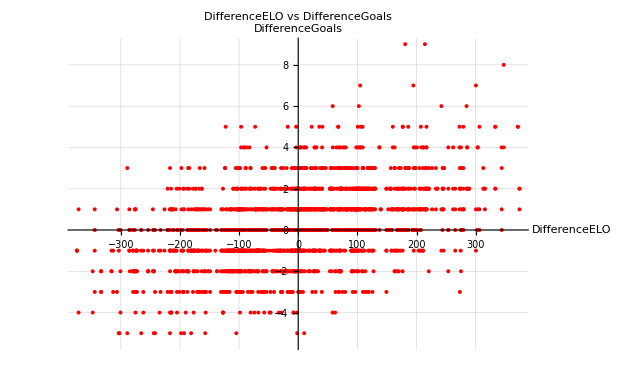

```mathematica
variablePredictor1 = "DifferenceELO";
variablePredictor2 = "";
variableResponse = "DifferenceGoals";

Show[
  ListPlot[Transpose[{dataDS[All,variablePredictor1]//Normal,dataDS[All,variableResponse]//Normal}], PlotStyle -> Red, 
   AxesLabel -> {variablePredictor1, variableResponse}, 
   PlotLabel -> variablePredictor1 <> " vs " <> variableResponse, 
   GridLines -> Automatic]
]
```

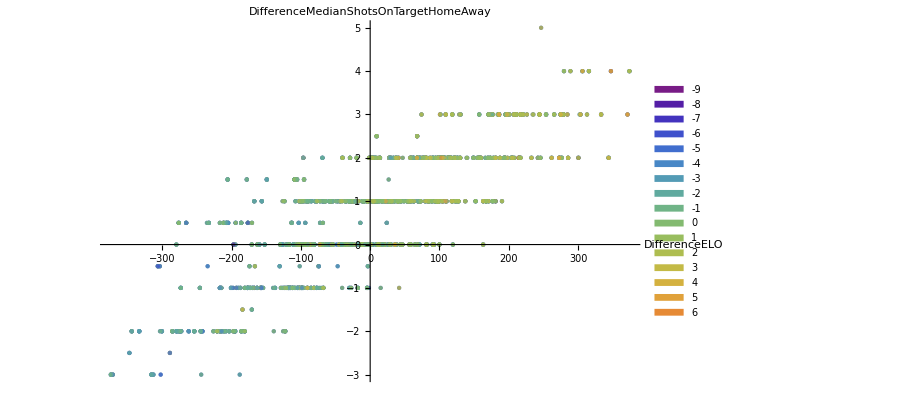

```mathematica
(* Variables predictoras y respuesta *)
variablePredictor1 = "DifferenceELO";
variablePredictor2 = "DifferenceShotsOnTargetHomeAway";
variableResponse = "DifferenceGoals";

(* Preparación de los datos para graficar *)
dataPlot = Transpose[{dataDS[All, variablePredictor1] // Normal, dataDS[All, variablePredictor2] // Normal, dataDS[All, variableResponse] // Normal}];

(* Valores únicos del response *)
uniqueValues = Sort[DeleteDuplicates[dataPlot[[All, 3]]]];
legendColors = ColorData["Rainbow"] /@ Rescale[uniqueValues, {Min[uniqueValues], Max[uniqueValues]}];

(* Crear el gráfico con ajustes de tamaño y transparencia *)
ListPlot[
    {
        Style[{#[[1]], #[[2]]}, ColorData["Rainbow"][Rescale[#[[3]], {Min[uniqueValues], Max[uniqueValues]}]], Opacity[0.7], PointSize[Medium]] & /@ dataPlot
    },
    PlotLegends -> Placed[
        SwatchLegend[legendColors, uniqueValues, LegendLayout -> "Column"],
        Right
    ],
    PlotRange -> {Automatic, Automatic},
    AxesLabel -> {variablePredictor1, variablePredictor2}
]
```

{{347.366,6.,8}}

{{194.651,4.,7},{300.457,2.33333,7},{104.731,2.6,7}}

{{180.842,2.25,9},{214.203,4.,9}}

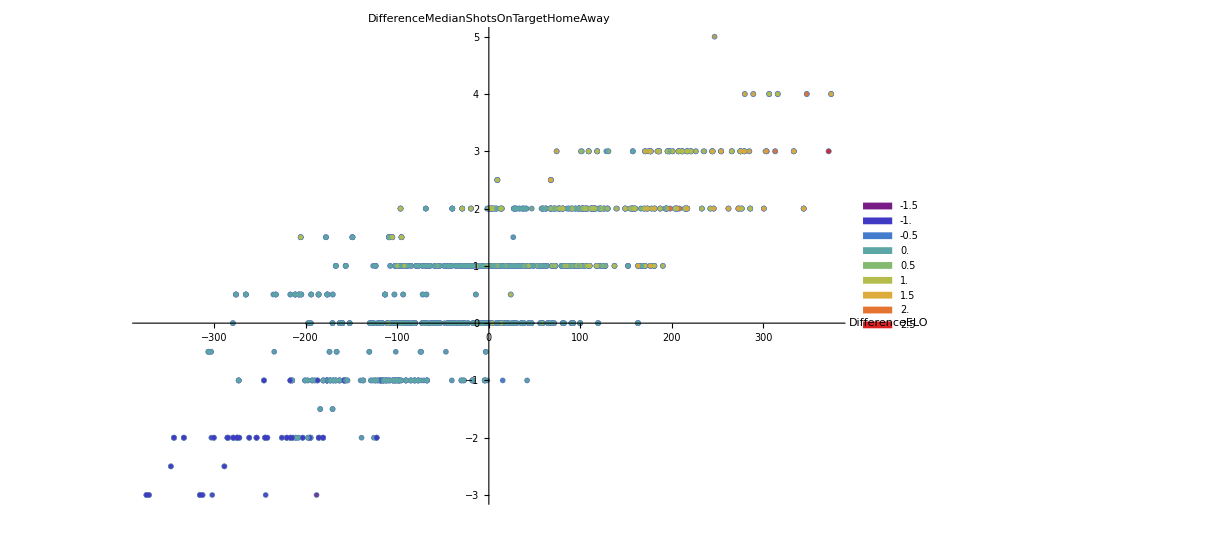

```mathematica
(*Buscar elementos con el tercer subelemento igual a 9,8 y 7*)elementos9=Select[dataPlot,#[[3]]==9&];
elementos8=Select[dataPlot,#[[3]]==8&]
elementos7=Select[dataPlot,#[[3]]==7&]
elementos9=Select[dataPlot,#[[3]]==9&]
```